Část na parametry

```mathematica
h = 1
V =1
```

1

1

```mathematica
x1 = 1
```

1

```mathematica
x2=1
```

1

Část na výpočet βstart, βend a čas

```mathematica
X2 =  h(-Sec[B]+Sec[β])
```

-Sec[B]+Sec[β]

```mathematica
X1 = 1/2 h(-ArcTanh[Sin[B]]+ArcTanh[Sin[β]]-Sec[B] Tan[B]+2 Sec[B] Tan[β]-Sec[β] Tan[β])
```

1/2 (-ArcTanh[Sin[B]]+ArcTanh[Sin[β]]-Sec[B] Tan[B]+2 Sec[B] Tan[β]-Sec[β] Tan[β])

```mathematica
Find
```

Find

```mathematica
res = FindRoot[{X1==x1,X2==x2},{{β,5/4Pi},{B,4}},PrecisionGoal->Infinity]
```

{β→4.19026,B→4.37315}

```mathematica
βend = B /.res
```

4.37315

```mathematica
βstart = β /. res
```

4.19026

```mathematica
t1 = -(h/V)(Tan[βstart]-Tan[βend])
```

1.0959

Kontrolní část

```mathematica
h(1/(Cos[βstart])-1/(Cos[βend]))
```

1.

```mathematica
1/2 h(-ArcTanh[Sin[βend]]+ArcTanh[Sin[βstart]]-Sec[βend] Tan[βend]+2 Sec[βend] Tan[βstart]-Sec[βstart] Tan[βstart])
```

1.

```mathematica
rce = {x'[t]==V*Cos[β[t]]-(V/h)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h)(Cos[β[t]])^2}
```

{x'[t]==Cos[β[t]]-y[t],y'[t]==Sin[β[t]],β'[t]==Cos[β[t]]^2}

```mathematica
sol1 = NDSolve[Join[rce,{x[0]==x1,y[0]==x2,β[0]==βstart}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
{x[t],y[t]}/.sol1
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

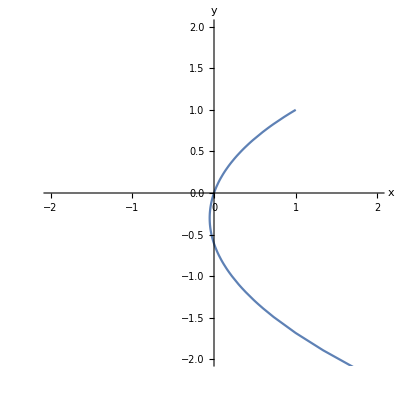

```mathematica
ParametricPlot[Table[{x[t],y[t]}/.sol1],{t,0,10},AxesLabel->{x,y},PlotRange->{{-2,2},{-2,2}}]
```